### Permittivity and optical index of gold as a function of λ (in nm) and temperature -T (in °C) (ref. Chen, Yu-Jen, Meng-Chang Lee, and Chih-Ming Wang. “Dielectric function dependence on temperature for Au and Ag.” Japanese Journal of Applied Physics 53.8S2 (2014): 08MG02.)

```mathematica
ϵDS[λ_,Ap_,Bp_,Cp_,T_,As_,Bs_,Cs_,A∞_,B∞_,C∞_]:=


(A∞+B∞*Exp[-1000/(C∞*(T+273.15))])-(((Ap+Bp*Exp[-1000/(Cp*(T+273.15))])^2)*((As+Bs*Exp[-1000/(Cs*(T+273.15))])^2))/(1+(((2*π*299792458)/(λ*10^-9))^2)*((As+Bs*Exp[-1000/(Cs*(T+273.15))])^2))+((Ap+Bp*Exp[-1000/(Cp*(T+273.15))])^2*(As+Bs*Exp[-1000/(Cs*(T+273.15))]))/(((2*π*299792458)/(λ*10^-9))+((2*π*299792458)/(λ*10^-9))^3*(As+Bs*Exp[-1000/(Cs*(T+273.15))])^2)ⅈ;
```

```mathematica
Ap= 1.39*10^16;
Bp=-6.33*10^16;
Cp=0.31;
As=5.96*10^-15;
Bs=-1.8*10^-14;
Cs=0.91;
A∞=26141;
B∞=-26133;
C∞=110740;

ϵAu[λ_ ,T_]:=ϵDS[λ,1.39*^16,-6.33*^16,0.31,T,5.96*^-15,-1.8*^-14,0.91,26141,-26133,110740];
nAu[λ_ ,T_]:=Sqrt[ϵAu[λ ,T]];
```

### Optical index of pure air as a function of λ (in nm) and temperature -T (in °C) and humidity - hu (in RH) and Pressure - P (in Pa) and CO_2 concentration - xu (in ppm) (ref: M. N. Polyanskiy, “Refractive index database,” https://refractiveindex.info. Accessed on 2018-02-01.)

```mathematica
nairAmbiant[λ_,T_,P_,hu_,xc_,a0_,a1_,a2_,b0_,b1_,c0_,c1_,d_,e_,R_,k0_,k1_,k2_,k3_,w0_,w1_,w2_,w3_,αair_,βair_,γair_]:=


Module[{svp,Za,Zw,ρaxs,ρws,ρa,ρw},svp=If[T≥0,Exp[1.2378847 *10^-5 *(T+273.15)^2-1.9121316 *10^-2* (T+273.15)+33.93711047(-6.343164 *10^+3)/(T+273.15)],10^(-2663.5/(T+273.15)+12.537)];


Za=1-1/(15+273.15)*101325 *1.58123 *10^-6+-2.9331 *10^-8*15+1.1043 *10^-10 *15^2+(5.707 *10^-6+-2.051 *10^-8 *15) (0)+(1.9898 *10^-4+-2.376 *10^-6* 15) (0)^2+(101325/(15+273.15))^2 (1.83 *10^-11+-0.765 *10^-8* (0)^2);
Zw = 1-1/(20+273.15)*1333 *1.58123 *10^-6+-2.9331 *10^-8*20+1.1043 *10^-10 *20^2+(5.707 *10^-6+-2.051 *10^-8 *20) (1)+(1.9898 *10^-4+-2.376 *10^-6* 20) (1)^2+(1333/(20+273.15))^2 (1.83 *10^-11+-0.765 *10^-8* (1)^2);

ρaxs=1/(Za *R *288.15)101325 *(1 *10^-3 *(28.9635+12.011 *10^-6 *(xc-400)));ρws=(1333 0.018015)/(Zw *R* 293.15);

ρa=(P*100)*(1*10^-3*(28.9635+12.011*10^-6*(xc-400)))/((1-((P*100)/(T+273.15))*(a0+a1*T+a2*T^2+(b0+b1*T)*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))+(c0+c1*T)*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))^2)+((P*100)/(T+273.15))^2*(d+e*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))^2))*R*(T+273.15))*(1-(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100)));

ρw=(P*100)*0.018015/((1-((P*100)/(T+273.15))*(a0+a1*T+a2*T^2+(b0+b1*T)*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))+(c0+c1*T)*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))^2)+((P*100)/(T+273.15))^2*(d+e*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100))^2))*R*(T+273.15))*(((αair+βair*(P*100)+γair*T^2)*hu*svp)/(P*100));

1+(ρa/ρaxs)*((1+((1+(k1/(k0-((1/(λ/1000))^2))+k3/(k2-((1/(λ/1000))^2)))*1*10^-8)-1)*(1+0.534*10^-6*(xc-450)))-1)+(ρw/ρws)*((1+1.022*(w0+w1*((1/(λ/1000))^2)+w2*((1/(λ/1000))^4)+w3*((1/(λ/1000))^6))*1*10^-8)-1)];
```

```mathematica
a0=1.58123 *10^-6;   (*K·Pa^-1*)
a1=-2.9331 *10^-8;   (*Pa^-1*)
a2=1.1043 *10^-10;   (*K^-1·Pa^-1*)
b0=5.707 *10^-6;   (*K·Pa^-1*)
b1=-2.051 *10^-8 ;  (*Pa^-1*)
c0=1.9898 *10^-4;   (*K·Pa^-1*)
c1=-2.376 *10^-6;   (*Pa^-1*)
d=1.83 *10^-11;   (*K^2·Pa^-2*)
e=-0.765 *10^-8;  (*K^2·Pa^-2*)
R=8.31451;   (*gas constant,J/(mol·K)*)
k0=238.0185;   (*μm^-2*)
k1=5792105;  (*μm^-2*)
k2=57.362;  (*μm^-2*)
k3=167917;  (*μm^-2*)
w0=295.235;  (*μm^-2*)
w1=2.6422;   (*μm^-2*)
w2=-0.03238;  (*μm^-4*)
w3=0.004028;  (*μm^-6*)
αair=1.00062;  
βair=3.14 *10^-8;  (*Pa^-1*)
γair=5.6 *10^-7;  (*°C^-2*)

(*λ:wavelength,0.3 to 1.69 μm;  tair:temperature,-40 to+100 °C; P:pressure,80000 to 120000 Pa; hu:fractional humidity,0 to 1; xc:Subscript[CO, 2] concentration,0 to 2000 ppm*)

nairAmbiant[λ_,T_,P_,hu_,xc_]:=nairAmbiant[λ,T,P,hu,xc,a0,a1,a2,b0,b1,c0,c1,d,e,R,k0,k1,k2,k3,w0,w1,w2,w3,αair,βair,γair];

ϵairAmbiant[λ_,T_,P_,hu_,xc_]:=nairAmbiant[λ,T,P,hu,xc]^2;
```

### The penetration depth - Lz (in nm) at proximity of the Au-air interface as a function of λ (in nm) and temperature - T (in °C) and humidity - hu (in RH) and Pressure - P (in Pa) and CO_2 concentration - xu (in ppm)

```mathematica
Lz[λ_,T_,P_,hu_,xc_]:=λ/(4*Pi*Abs[Im[ϵairAmbiant[λ,T,P,hu,xc]/Sqrt[ϵairAmbiant[λ,T,P,hu,xc]+ϵAu[λ ,T]]]]);
(*The penetration depth  calculation*)
N[Lz[632.8,25,101350, 0,1]]
```

165.291

### SPR-based Quantitative Receptor Density equation as a function of λ (in nm) and temperature - T (in °C) and humidity - hu (in RH) and Pressure - P (in Pa) and CO_2 concentration - xu (in ppm) and molecular mass of probe - M (in gmol^-1) and A (in molg^-1) and Refractive Index Sensitivity - RIUSens (in %RIU^-1) and Reflectivity - ΔR (in %)

```mathematica
σpeptide[λ_,T_,P_,hu_,xc_,NA_,R_,M_,A_,P0_,RIUSens_,ΔR_]:=

Module[{Lz,RIU,V0},

Lz=λ/(4*Pi*Abs[Im[ϵairAmbiant[λ,T,P,hu,xc]/Sqrt[ϵairAmbiant[λ,T,P,hu,xc]+ϵAu[λ ,T]]]])*10^{-9};

RIU=ΔR/RIUSens;

V0=(R*(T+273.15))/P0;

RIU*(NA*Lz)/(A*10^{-6}*M*V0)*10^{-18}];
(*10^{-18} convert m^-2 to nm^-2*)

NA= 6.022*10^23;(*Avogadro’s number*)
R=8.314; (*gas constant,J/(mol·K)*)
P0= 101350 ;(*Pa*)

σpeptide[λ_,T_,P_,hu_,xc_,M_,A_,RIUSens_,ΔR_]:=σpeptide[λ,T,P,hu,xc,NA,R,M,A,P0,RIUSens,ΔR];
```

```mathematica
(*λ:wavelength-632.8 μm;  tair:temperature-25 °C; P:pressure-101350 Pa; hu:fractional humidity-0 ; xc:Subscript[CO, 2] concentration-1 ppm M:arbitary Moar mass-1000 amu;  RIUSens: Refractive Index Sensitivity-6500 %RIU^-1*)
```

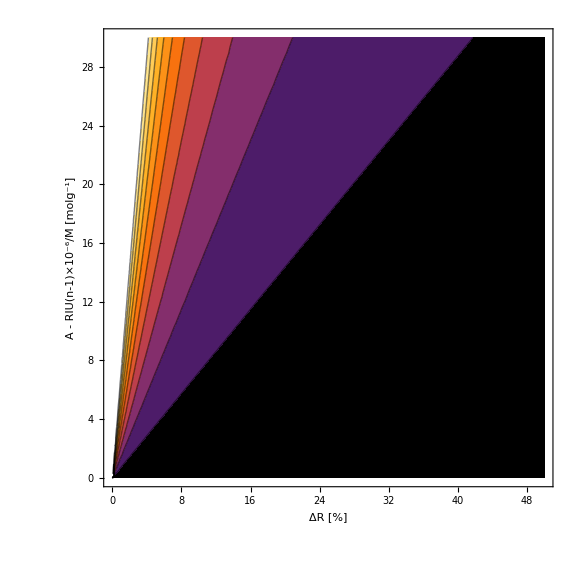

```mathematica
λ = 632.8; (*nm*)
T=25; (*°C*)
P =101350 ;(*Pa*)
hu=0 ;(*RH*)
xu = 1; (*ppm*)
M=1000 ;(*g·mol^-1*)
RIUSens = 6500;(*%RIU^-1*)

Show[ContourPlot[σpeptide[λ,T,P,hu,xu,M,A,RIUSens ,ΔR],{A,0,50},{ΔR,0,30},Contours-> 10,PlotRange->{{0,50},{0,30},{0,5}},ColorFunction->"SunsetColors",ColorFunction->Automatic,
FrameLabel->{{"A - RIU(n-1)×10^-6/M [molg^-1]",None},{"ΔR [%]",None}},Frame->True,FrameTicks->{True,True,True,True},ImageSize->Large,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial Unicode MS",FontSize->20,FontColor->Black},LabelStyle->{25,Black},AspectRatio->1,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"σ_peptide[nm^-2]",LabelStyle->{FontFamily->"Arial Unicode MS",FontSize->20,FontColor->Black},LegendMarkerSize->250, LegendLayout->"Row"],Top]]]
```